## New

```mathematica
MM=3;NN=2;
(B=RandomInteger[{1,1000},{MM,NN}])//TableForm
B[[3,1]]
Log@N@Sum[B[[i,NN]]/Sum[B[[i,j]],{j,1,NN}],{i,1,MM}]
```

291 | 162
37 | 574
625 | 613

625

0.583451

```mathematica
Table[{B=RandomInteger[{1,1000},{m,n}],Log@N@Sum[B[[i,1]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{c,1,2}][[;;,2]]/.{m->10,n->3}
```

{1.23664,1.24103}

```mathematica
DeltaS[m_,n_]:=Table[{B=RandomInteger[{1,1000},{m,n}],Log@N@Sum[B[[i,1]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{c,1,100000}][[;;,2]];
```

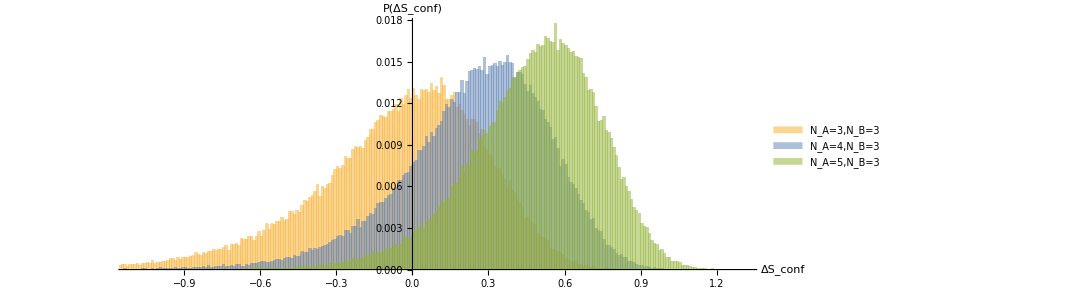

```mathematica
H=Histogram[{DeltaS[3,3],DeltaS[4,3],DeltaS[5,3]},{0.01},"Probability",AxesLabel->{Style["ΔS_conf",FontSize->22, Bold,Background->White,FontFamily->"Latin Modern Math"],Style["P(ΔS_conf)",FontSize->22, Bold,FontFamily->"Latin Modern Math"]},ImageSize->{800,300},AspectRatio->3/8,AxesStyle-> Directive[FontSize->18, FontFamily->"Latin Modern Math"],ChartLegends->Placed[{Style["N_A=3,N_B=3",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=4,N_B=3",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=5,N_B=3",FontSize->22, FontFamily->"Latin Modern Math"]},Bottom],AxesOrigin->{0,0}]
```

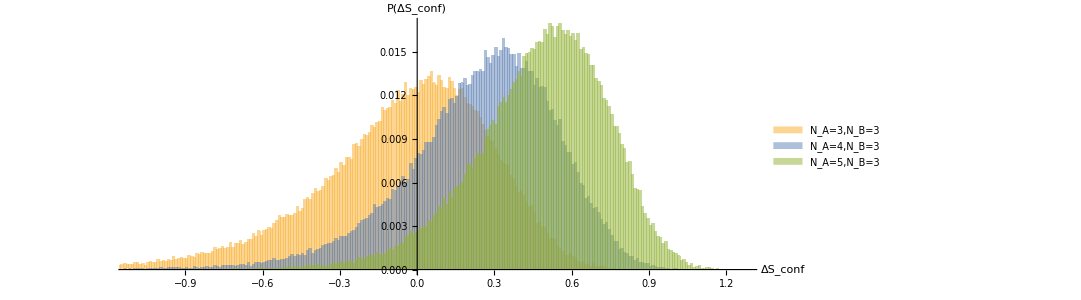

/Users/masteranza/Projects/MasterThesis/Work/Poster/Figure2.eps

```mathematica
Export[NotebookDirectory[]<>"Figure2.eps",H]
```

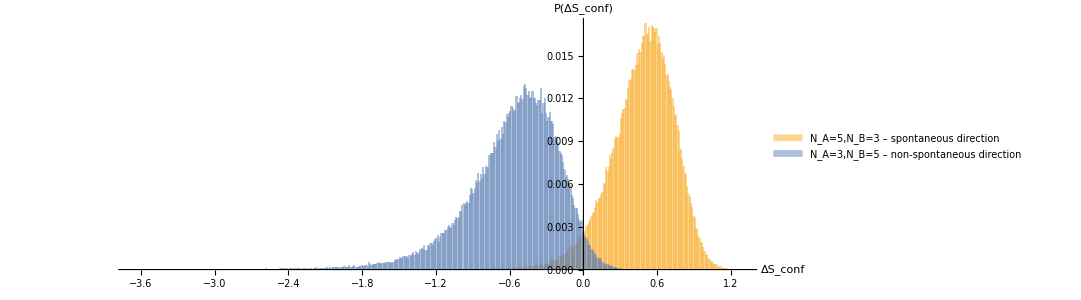

/Users/masteranza/Projects/MasterThesis/Work/Poster/Figure3.eps

```mathematica
H=Histogram[{DeltaS[5,3],DeltaS[3,5]},{0.01},"Probability",AxesLabel->{Style["ΔS_conf",FontSize->22, Bold,Background->White,FontFamily->"Latin Modern Math"],Style["P(ΔS_conf)",FontSize->22, Bold,FontFamily->"Latin Modern Math"]},ImageSize->{800,300},AspectRatio->3/8,AxesStyle-> Directive[FontSize->18, FontFamily->"Latin Modern Math"],ChartLegends->Placed[{Style["N_A=5,N_B=3 – spontaneous direction",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=3,N_B=5 – non-spontaneous direction",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=5,N_B=3",FontSize->22, FontFamily->"Latin Modern Math"]},Bottom],AxesOrigin->{0,0}]
Export[NotebookDirectory[]<>"Figure3.eps",H]
```

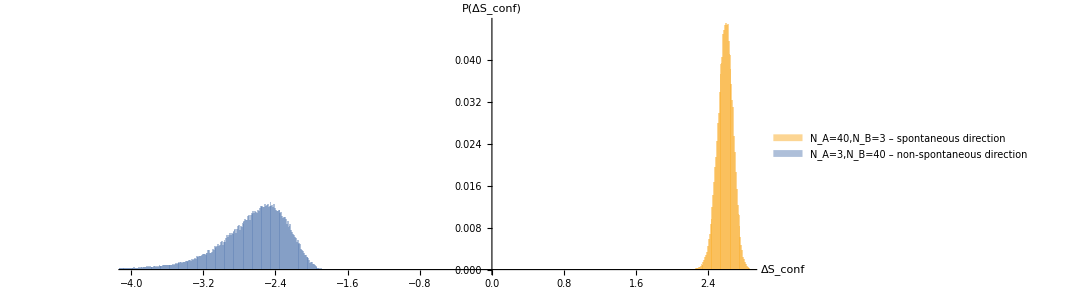

/Users/masteranza/Projects/MasterThesis/Work/Poster/Figure4.eps

```mathematica
H=Histogram[{DeltaS[40,3],DeltaS[3,40]},{0.01},"Probability",AxesLabel->{Style["ΔS_conf",FontSize->22, Bold,Background->White,FontFamily->"Latin Modern Math"],Style["P(ΔS_conf)",FontSize->22, Bold,FontFamily->"Latin Modern Math"]},ImageSize->{800,300},AspectRatio->3/8,AxesStyle-> Directive[FontSize->18, FontFamily->"Latin Modern Math"],ChartLegends->Placed[{Style["N_A=40,N_B=3 – spontaneous direction",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=3,N_B=40 – non-spontaneous direction",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=40,N_B=3",FontSize->22, FontFamily->"Latin Modern Math"]},Bottom],AxesOrigin->{0,0},PlotRangeClipping->True,PlotRange->{{-4,2.8},All}]
Export[NotebookDirectory[]<>"Figure4.eps",H]
```

```mathematica
H=Histogram[{DeltaS[40,3],DeltaS[3,40]},{0.01},"Probability",AxesLabel->{Style["ΔS_conf",FontSize->22, Bold,Background->White,FontFamily->"Latin Modern Math"],Style["P(ΔS_conf)",FontSize->22, Bold,FontFamily->"Latin Modern Math"]},ImageSize->{800,300},AspectRatio->3/8,AxesStyle-> Directive[FontSize->18, FontFamily->"Latin Modern Math"],ChartLegends->Placed[{Style["N_A=40,N_B=3 – spontaneous direction",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=3,N_B=40 – non-spontaneous direction",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=40,N_B=3",FontSize->22, FontFamily->"Latin Modern Math"]},Bottom],AxesOrigin->{0,0}]
Export[NotebookDirectory[]<>"Figure4.eps",H]
```

## Poisson New

```mathematica
DeltaS[m_,n_]:=Table[{B=Table[RandomVariate[PoissonDistribution[500],n],m],Log@N@Sum[B[[i,n]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{i,1,100000}][[;;,2]];
```

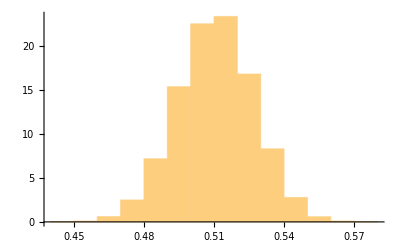

```mathematica
Histogram[DeltaS[5,3],{0.01},"PDF"]
```

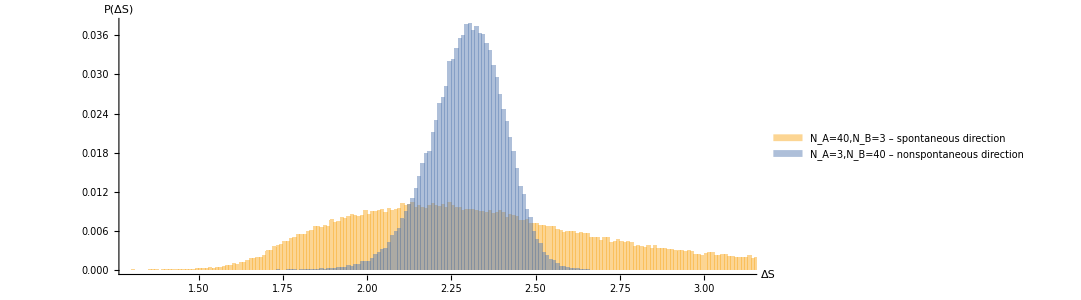

```mathematica
H=Histogram[{-DeltaS[2,20],DeltaS[20,2]},{0.01},"Probability",AxesLabel->{Style["ΔS",FontSize->22, Bold,Background->White,FontFamily->"Latin Modern Math"],Style["P(ΔS)",FontSize->22, Bold,FontFamily->"Latin Modern Math"]},ImageSize->{800,300},AspectRatio->3/8,AxesStyle-> Directive[FontSize->18, FontFamily->"Latin Modern Math"],ChartLegends->Placed[{Style["N_A=40,N_B=3 – spontaneous direction",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=3,N_B=40 – nonspontaneous direction",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=40,N_B=3",FontSize->22, FontFamily->"Latin Modern Math"]},Bottom],AxesOrigin->{0,0}]
```

## Old idea for open systems

```mathematica
(B=RandomInteger[{1,1000},{5,6}])//TableForm
```

901 | 10 | 446 | 221 | 380 | 812
756 | 163 | 872 | 964 | 538 | 183
445 | 283 | 528 | 936 | 387 | 545
644 | 833 | 652 | 771 | 502 | 44
382 | 485 | 61 | 505 | 803 | 5

```mathematica
B[[;;,1;;3]]//TableForm
```

901 | 10 | 446
756 | 163 | 872
445 | 283 | 528
644 | 833 | 652
382 | 485 | 61

```mathematica
Length@B[[,;;]]
```

3

```mathematica
Loss[B_,prepercent_,percent_]:=B[[1;;Round[(1-prepercent)Length@B ],1;;Round[(1-percent)Length@B[[1,;;]] ] ]];
```

```mathematica
Loss[B,0.1]
```

{{901,10,446,221,380,812}}

```mathematica
Loss[RandomInteger[{1,1000},{6,5}],0.1]
```

{{120,248,229,597},{364,660,185,341},{636,691,85,878},{875,432,494,91},{745,139,419,928},{785,104,668,861}}

```mathematica
DeltaS[m_,n_,prepercent_, prepercent2_, percent_,percent2_]:=Table[{B=RandomInteger[{1,1000},{m,n}],Log@N@Sum[Loss[B,prepercent,percent][[i,1]]/Sum[Loss[B,prepercent,percent][[i,j]],{j,1,Round[(1-percent)n]}],{i,1,Round[(1-prepercent)n]}],-Log@N@Sum[Loss[Bᵀ,prepercent2, percent2][[i,1]]/Sum[Loss[Bᵀ,prepercent2, percent2][[i,j]],{j,1,Round[(1-percent2)m]}],{i,1,Round[(1-prepercent2)n]}]},{c,1,1000}][[;;,{2,3}]]ᵀ;
```

```mathematica
Histo[m_,n_,prepercent_,prepercent2_,percent_,percent2_]:=Histogram[DeltaS[m,n,percent,percent2],{0.01},"Probability",AxesLabel->{Style["ΔS_conf",FontSize->22, Bold,Background->White,FontFamily->"Latin Modern Math"],Style["P(ΔS_conf)",FontSize->22, Bold,FontFamily->"Latin Modern Math"]},ImageSize->{800,300},AspectRatio->3/8,AxesStyle-> Directive[FontSize->18, FontFamily->"Latin Modern Math"],ChartLegends->Placed[{Style["N_A="<>ToString[m]<>" lost to "<>ToString[Round[(1-prepercent)m]]<>",N_B="<>ToString[n]<>" lost to "<>ToString[Round[(1-percent)n]],FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A="<>ToString[n]<>" lost to "<>ToString[Round[(1-prepercent2)n]]<>",N_B="<>ToString[m]<>" lost to " <> ToString[Round[(1-percent2)m]],FontSize->22, FontFamily->"Latin Modern Math"]},Bottom],AxesOrigin->{0,0}];
```

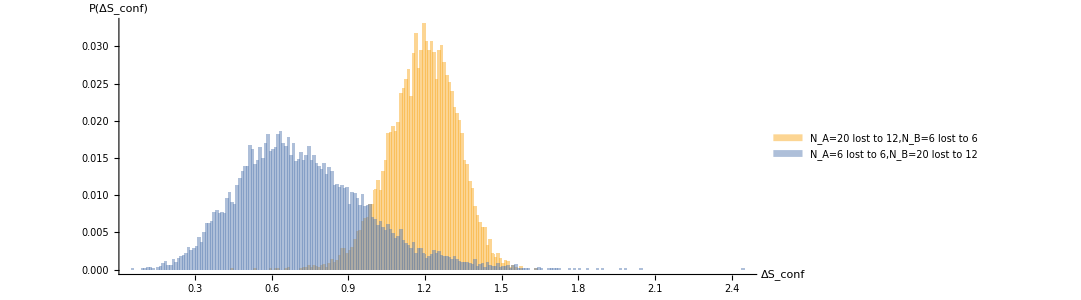

```mathematica
Histo[20,6,0.4,0,0,0.4]
```

## NEW IDEA!

```mathematica
DeltaS[m_,n_,microstates_]:=Table[{B=RandomInteger[{1,microstates},{m,n}],Log@N@Sum[B[[i,1]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{c,1,10000}][[;;,2]];
```

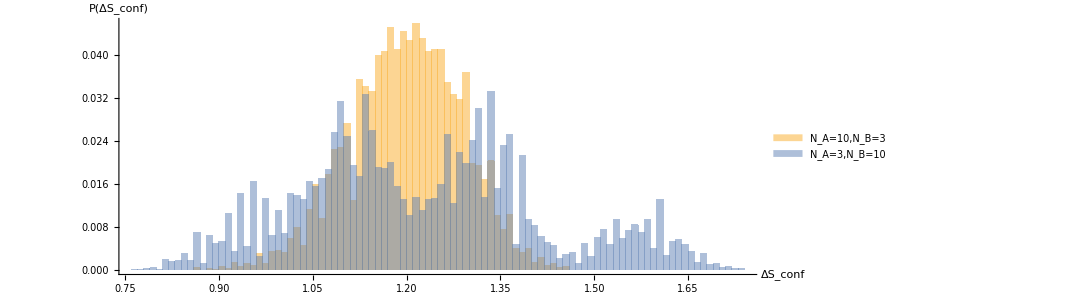

```mathematica
Histo[m_,n_,micro1_,micro2_]:=Histogram[{DeltaS[m,n,micro1],-DeltaS[n,m,micro2]},{0.01},"Probability",AxesLabel->{Style["ΔS_conf",FontSize->22, Bold,Background->White,FontFamily->"Latin Modern Math"],Style["P(ΔS_conf)",FontSize->22, Bold,FontFamily->"Latin Modern Math"]},ImageSize->{800,300},AspectRatio->3/8,AxesStyle-> Directive[FontSize->18, FontFamily->"Latin Modern Math"],ChartLegends->Placed[{Style["N_A="<>ToString[m]<>",N_B="<>ToString[n],FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A="<>ToString[n]<>",N_B="<>ToString[m],FontSize->22, FontFamily->"Latin Modern Math"]},Bottom],AxesOrigin->{0,0}]
Histo[10,3,2,2]
```

```mathematica
Export[NotebookDirectory[]<>"Figure2.eps",H]
```

## Macrostates instead of microstates?

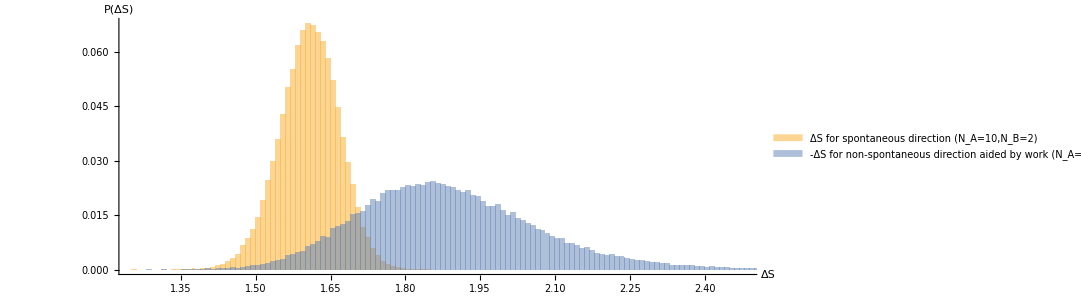

/Users/masteranza/Projects/MasterThesis/Work/Poster/Figure6.eps

```mathematica
DeltaS[m_,n_]:=Table[{B=RandomInteger[{1,1000},{m,n}],Log@N@Sum[B[[i,1]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{c,1,100000}][[;;,2]];
H=Histogram[{DeltaSGauss[10,2],-DeltaSGauss[2,13]},{0.01},"Probability",AxesLabel->{Style["ΔS",FontSize->22, Bold,Background->White,FontFamily->"Latin Modern Math"],Style["P(ΔS)",FontSize->22, Bold,FontFamily->"Latin Modern Math"]},ImageSize->{800,300},AspectRatio->3/8,AxesStyle-> Directive[FontSize->18, FontFamily->"Latin Modern Math"],ChartLegends->Placed[{Style["ΔS for spontaneous direction (N_A=10,N_B=2)",FontSize->22, FontFamily->"Latin Modern Math"],Style["-ΔS for non-spontaneous direction aided by work (N_A=2,N_B=13)",FontSize->22, FontFamily->"Latin Modern Math"]},Bottom],AxesOrigin->{0,0}]
Export[NotebookDirectory[]<>"Figure6.eps",H]
```

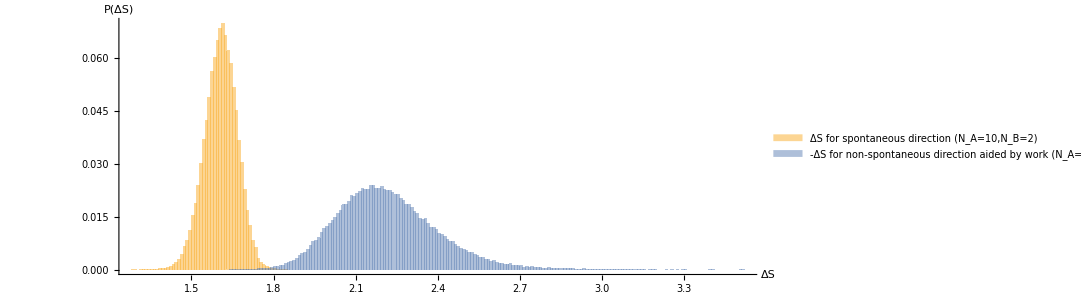

/Users/masteranza/Projects/MasterThesis/Work/Poster/Figure7.eps

```mathematica
DeltaS[m_,n_]:=Table[{B=RandomInteger[{1,1000},{m,n}],Log@N@Sum[B[[i,1]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{c,1,100000}][[;;,2]];
H=Histogram[{DeltaSGauss[10,2],-DeltaSGauss[2,18]},{0.01},"Probability",AxesLabel->{Style["ΔS",FontSize->22, Bold,Background->White,FontFamily->"Latin Modern Math"],Style["P(ΔS)",FontSize->22, Bold,FontFamily->"Latin Modern Math"]},ImageSize->{800,300},AspectRatio->3/8,AxesStyle-> Directive[FontSize->18, FontFamily->"Latin Modern Math"],ChartLegends->Placed[{Style["ΔS for spontaneous direction (N_A=10,N_B=2)",FontSize->22, FontFamily->"Latin Modern Math"],Style["-ΔS for non-spontaneous direction aided by work (N_A=2,N_B=18)",FontSize->22, FontFamily->"Latin Modern Math"]},Bottom],AxesOrigin->{0,0}]
Export[NotebookDirectory[]<>"Figure7.eps",H]
```

## Additiveness

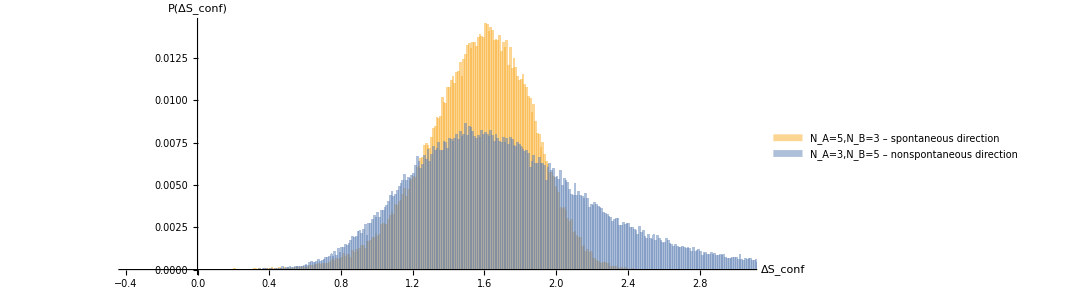

```mathematica
DeltaS[m_,n_]:=Table[{B=RandomInteger[{1,1000},{m,n}],Log@N@Sum[B[[i,1]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{c,1,100000}][[;;,2]];
H=Histogram[{DeltaS[10,5]+DeltaS[5,2],-(DeltaS[2,5]+DeltaS[5,10])},{0.01},"Probability",AxesLabel->{Style["ΔS_conf",FontSize->22, Bold,Background->White,FontFamily->"Latin Modern Math"],Style["P(ΔS_conf)",FontSize->22, Bold,FontFamily->"Latin Modern Math"]},ImageSize->{800,300},AspectRatio->3/8,AxesStyle-> Directive[FontSize->18, FontFamily->"Latin Modern Math"],ChartLegends->Placed[{Style["N_A=5,N_B=3 – spontaneous direction",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=3,N_B=5 – nonspontaneous direction",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=5,N_B=3",FontSize->22, FontFamily->"Latin Modern Math"]},Bottom],AxesOrigin->{0,0}]
```

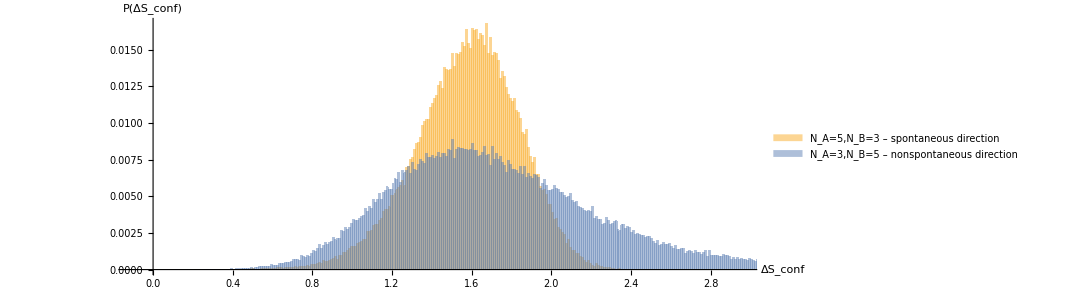

```mathematica
DeltaS[m_,n_]:=Table[{B=RandomInteger[{1,1000},{m,n}],Log@N@Sum[B[[i,1]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{c,1,100000}][[;;,2]];
H=Histogram[{DeltaS[10,9]+DeltaS[9,2],-(DeltaS[2,5]+DeltaS[5,10])},{0.01},"Probability",AxesLabel->{Style["ΔS_conf",FontSize->22, Bold,Background->White,FontFamily->"Latin Modern Math"],Style["P(ΔS_conf)",FontSize->22, Bold,FontFamily->"Latin Modern Math"]},ImageSize->{800,300},AspectRatio->3/8,AxesStyle-> Directive[FontSize->18, FontFamily->"Latin Modern Math"],ChartLegends->Placed[{Style["N_A=5,N_B=3 – spontaneous direction",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=3,N_B=5 – nonspontaneous direction",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=5,N_B=3",FontSize->22, FontFamily->"Latin Modern Math"]},Bottom],AxesOrigin->{0,0}]
```

## Gaussian

```mathematica
DeltaSGauss[m_,n_]:=Table[{B=Table[Table[RandomVariate[NormalDistribution[1000,250]],{i,1,m}],{j,1,n}]ᵀ,Log@N@Sum[B[[i,1]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{c,1,100000}][[;;,2]];
```

```mathematica
DeltaSGauss[m_,n_]:=Block[{B},
Table[B=RandomVariate[NormalDistribution[100,250],{m,n}];
Log@N@Sum[B[[i,1]]*1.0/Sum[B[[i,j]],{j,1,n}],{i,1,m}],{c,1,10000}]
];
```

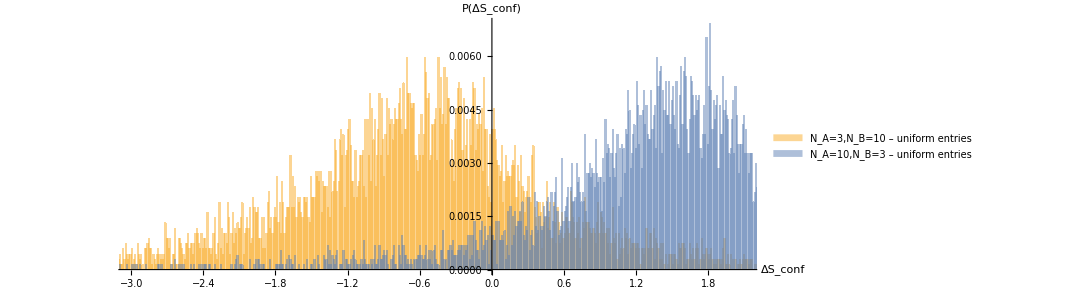

```mathematica
H=Histogram[{DeltaSGauss[3,10],DeltaSGauss[10,3]},{0.01},"Probability",AxesLabel->{Style["ΔS_conf",FontSize->22, Bold,Background->White,FontFamily->"Latin Modern Math"],Style["P(ΔS_conf)",FontSize->22, Bold,FontFamily->"Latin Modern Math"]},ImageSize->{800,300},AspectRatio->3/8,AxesStyle-> Directive[FontSize->18, FontFamily->"Latin Modern Math"],ChartLegends->Placed[{Style["N_A=3,N_B=10 – uniform entries",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=10,N_B=3 – uniform entries",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=3,N_B=10 – gaussian entries",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=10,N_B=3 - gaussian entries",FontSize->22, FontFamily->"Latin Modern Math"]},Bottom],AxesOrigin->{0,0},PlotRangeClipping->True,PlotRange->{{-3,2.1},All}]
```

```mathematica
DeltaSGauss[2,3]
```

{{-48.4398,232.559,-143.234},{305.148,-56.1212,88.256}}

```mathematica
DeltaS[m_,n_]:=Table[{B=RandomInteger[{1,2000},{m,n}],Log@N@Sum[B[[i,1]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{c,1,100000}][[;;,2]];
H=Histogram[{DeltaS[3,10],DeltaS[10,3],DeltaSGauss[3,10],DeltaSGauss[10,3]},{0.01},"Probability",AxesLabel->{Style["ΔS_conf",FontSize->22, Bold,Background->White,FontFamily->"Latin Modern Math"],Style["P(ΔS_conf)",FontSize->22, Bold,FontFamily->"Latin Modern Math"]},ImageSize->{800,300},AspectRatio->3/8,AxesStyle-> Directive[FontSize->18, FontFamily->"Latin Modern Math"],ChartLegends->Placed[{Style["N_A=3,N_B=10 – uniform entries",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=10,N_B=3 – uniform entries",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=3,N_B=10 – gaussian entries",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=10,N_B=3 - gaussian entries",FontSize->22, FontFamily->"Latin Modern Math"]},Bottom],AxesOrigin->{0,0},PlotRangeClipping->True,PlotRange->{{-3,2.1},All}]
Export[NotebookDirectory[]<>"Figure5.eps",H]
```

$Aborted

/Users/masteranza/Projects/MasterThesis/Work/Poster/Figure5.eps

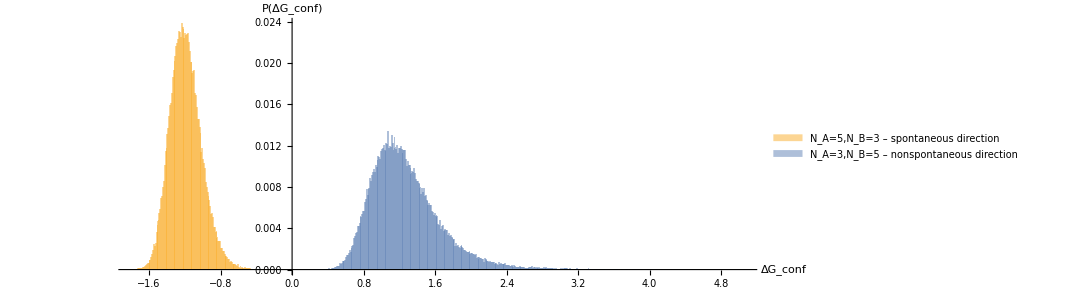

```mathematica
DeltaS[m_,n_]:=Table[{B=RandomInteger[{1,1000},{m,n}],-Log@N@Sum[B[[i,1]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{c,1,100000}][[;;,2]];
H=Histogram[{DeltaS[10,3],DeltaS[3,10]},{0.01},"Probability",AxesLabel->{Style["ΔG_conf",FontSize->22, Bold,Background->White,FontFamily->"Latin Modern Math"],Style["P(ΔG_conf)",FontSize->22, Bold,FontFamily->"Latin Modern Math"]},ImageSize->{800,300},AspectRatio->3/8,AxesStyle-> Directive[FontSize->18, FontFamily->"Latin Modern Math"],ChartLegends->Placed[{Style["N_A=5,N_B=3 – spontaneous direction",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=3,N_B=5 – nonspontaneous direction",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=5,N_B=3",FontSize->22, FontFamily->"Latin Modern Math"]},Bottom],AxesOrigin->{0,0}]
```

P_F/P_R=ⅇ^(β(W-ΔG))

P_F/P_R=ⅇ^-βΔG

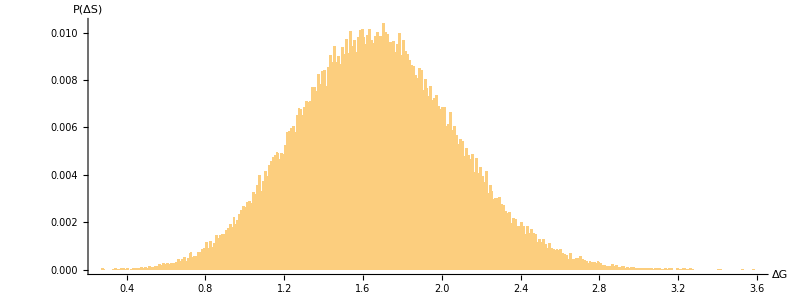

```mathematica
Histogram[Table[B=RandomInteger[{1,1000},{5,3}];N@Sum[B[[i,1]]*1.0/Sum[B[[i,j]],{j,1,3}],{i,1,5}],{c,1,100000}],{0.01},"Probability",AxesLabel->{"ΔG","P(ΔS)"},ImageSize->{800,300},AspectRatio->3/8,AxesStyle-> Directive[FontSize->18, FontFamily->"Latin Modern Math"],AxesOrigin->{0,0}]
```

```mathematica
.
```

```mathematica
DeltaS[m_,n_,work_]:=Block[{B},
Table[B=RandomInteger[{1,1000+work},{m,n}];-Log@N@Sum[B[[i,1]]*1.0/Sum[B[[i,j]],{j,1,n}],{i,1,m}],{c,1,10000}]];
```

```mathematica
DeltaSGauss[m_,n_]:=Block[{B},
Table[B=RandomVariate[NormalDistribution[1000,250],{m,n}];
Log@N@Sum[B[[i,1]]*1.0/Sum[B[[i,j]],{j,1,n}],{i,1,m}],{c,1,100000}]
];
```

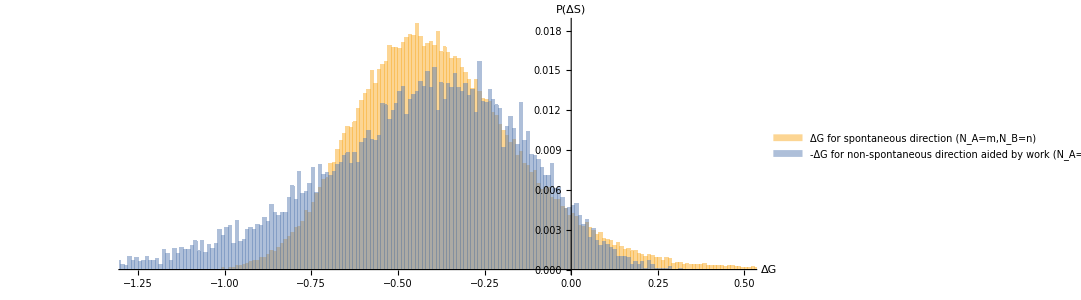

```mathematica
Histogram[{DeltaS[6,4],-DeltaS[4,6,0]},{0.01},"Probability",AxesLabel->{"ΔG","P(ΔS)"},ImageSize->{800,300},AspectRatio->3/8,AxesStyle-> Directive[FontSize->18, FontFamily->"Latin Modern Math"],ChartLegends->Placed[{Style["ΔG for spontaneous direction (N_A="<>ToString[m]<>",N_B="<>ToString[n]<>")",FontSize->22, FontFamily->"Latin Modern Math"],Style["-ΔG for non-spontaneous direction aided by work (N_A="<>ToString[nR]<>",N_B="<>ToString[mR]<>")",FontSize->22, FontFamily->"Latin Modern Math"]},Bottom],AxesOrigin->{0,0}]
```

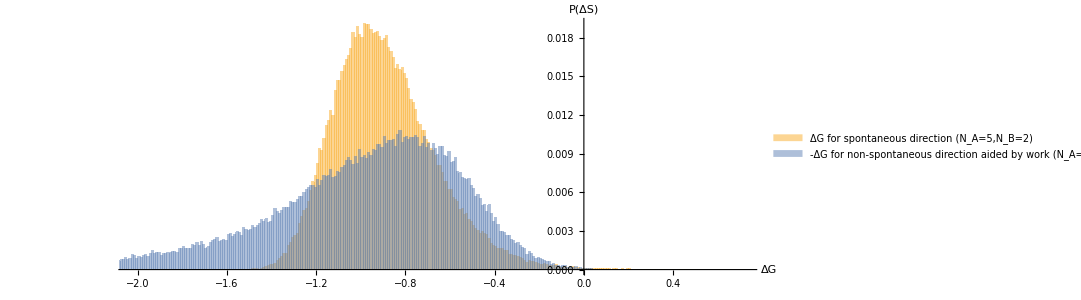

```mathematica
PlotHist[5,2,5,2]
```

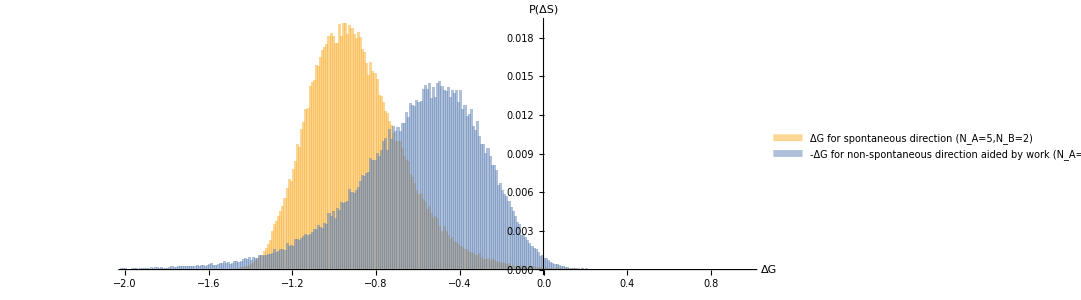

```mathematica
PlotHist[5,2,7,4]
```

```mathematica
aa=BinCounts[-DeltaSGauss[10,2],{-5,0.01,0.01}];
bb=BinCounts[DeltaSGauss[2,10],{-5,0.01,0.01}];
```

```mathematica
aa=BinCounts[-DeltaS[40,5],{-2.2,-1.8,0.01}];
bb=BinCounts[DeltaS[9,40],{-2.2,-1.8,0.01}];
```

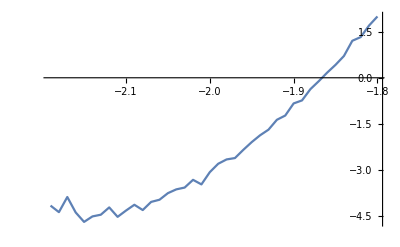

```mathematica
ListLinePlot[Table[{0.01*i-2.2,-Log[aa[[i]]/bb[[i]]]},{i,1,Length@aa}]]
```

```mathematica
H=Histogram[{DeltaS[10,3],DeltaS[3,10]},{0.01},"Probability",AxesLabel->{Style["ΔS_conf",FontSize->22, Bold,Background->White,FontFamily->"Latin Modern Math"],Style["P(ΔS_conf)",FontSize->22, Bold,FontFamily->"Latin Modern Math"]},ImageSize->{800,300},AspectRatio->3/8,AxesStyle-> Directive[FontSize->18, FontFamily->"Latin Modern Math"],ChartLegends->Placed[{Style["N_A=5,N_B=3 – spontaneous direction",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=3,N_B=5 – nonspontaneous direction",FontSize->22, FontFamily->"Latin Modern Math"],Style["N_A=5,N_B=3",FontSize->22, FontFamily->"Latin Modern Math"]},Bottom],AxesOrigin->{0,0}]
```

```mathematica
bb=BinLists[-DeltaSGauss[2,10],0.01];
```

```mathematica
aa//Short
```

{{-8.31262},{},{},«14»,{8.54492,8.1843},{9.11995},{10.1671}}

```mathematica
bbb=Length@#&/@bb/Total[Length@#&/@bb];
```

```mathematica
aaa=Length@#&/@aa/Total[Length@#&/@aa];
```

```mathematica
aa[[13;14]];
bb[[35;35]];
```

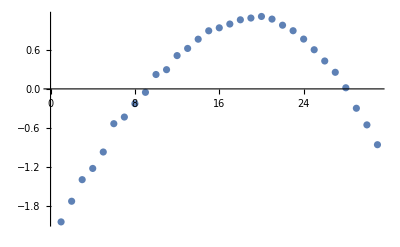

```mathematica
ListPlot@Table[Log[aaa[[13;;43]][[i]](1/bbb[[35;;65]][[i]])],{i,1,Length@aa}]
```